# Lista 02 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

## 1.

Um pêndulo consiste de um fio de massa desprezível e comprimento ℓ e de uma esfera de massa 𝓂  e raio muito menor que ℓ, na presença de uma aceleração da gravidade local ℊ e frente a uma resistência do ar desprezível. No limite de pequenas oscilações, o período do pêndulo é dado por T_0 = 2 π √(ℓ/ℊ), mas esse resultado vale apenas quando o ângulo máximo de oscilação é θ_0 << 1 rad. Fora desse limite, considerações baseadas na conservação da energia mecânica mostram que o período do pêndulo é dado por:
T = √((8 ℓ)/ℊ)∫_0^θ_0 ⅆθ/(√(Cosθ - Cosθ_0)) 
Faça um gráfico da razão entre esse período e o resultado de pequenas oscilações, desde θ_0 = 0 até θ_0 = 0.99 π.

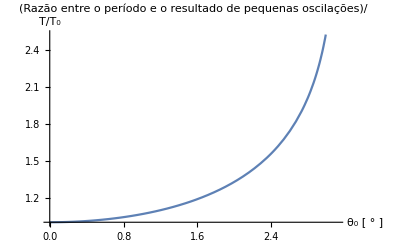

```mathematica
(*Definindo a função T (Subscript[θ, 0])*)
integral= Integrate[1/(√(Cos[θ] - Cos[x])),{θ, 0 , x}];
T[x_] := √((8 ℓ)/ℊ)*integral
Subscript[T, 0] = 2 π √(ℓ/ℊ);
(*Plotando o gráfico*)
Plot[T[x]/Subscript[T, 0], {x, 0, 0.99 π},PlotLabel->" Razão entre o período e o resultado de pequenas oscilações"/"",LabelStyle->{Black},AxesLabel->{HoldForm[Subscript[θ, 0]"["°"]"],HoldForm[T/Subscript[T, 0]]}]
```

## 2.

Para o circuito da figura abaixo, desprezando as resistências internas dos fios e das baterias,
• Com base nas leis de Kirchoff, determine as correntes percorrendo todos os resistores em termos das forças eletromotrizes E_1 e E_2 e das resistências R_1 a  R_6;
• Obtenha valores numéricos para as correntes quando E_1 = 12 V e E_2 = 8 V, R_1= 20.0 Ω , R_2= 15.0 Ω , R_3= 3.0 Ω , R_4= 6.0 Ω , R_5= 12.0 Ω  e  R_6= 2.0 Ω .
-Graphics-

```mathematica
(*Lei de malhas*) 
eq1 =E1 == (R1*I1) + (R2*I2) + (R3*I3);
eq2=E2 ==-(R3*I3) + (R4*I4) + (R6*I6);
eq3 = 0 == (R4*I4) + (R2*I2) - (R5*I5);
(*Lei dos Nós*)
eq4 = I6 ==I4 + I5;
eq5=I2==I3 + I4;
eq6 = I1== I2 + I5;
```

```mathematica
(*Determinando as equações*)
sols=Solve[{eq1,eq2,eq3, eq4,eq5,eq6},{I1,I2,I3,I4,I5,I6}]
```

{{I1→-(-E1 R2 R3-E2 R2 R3-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E1 R3 R5-E2 R3 R5-E1 R4 R5-E1 R2 R6-E1 R4 R6-E1 R5 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6),I2→-(E2 R5 (R1 R4-R3 R5)-E1 R5 (R3 R5+R4 R6+R5 (R4+R6)))/((R1 R4-R3 R5) (-R2 R6-R4 R6-R5 (R4+R6))-(-R1 R2-R1 R4-(R1+R2) R5) (R3 R5+R4 R6+R5 (R4+R6))),I3→-(E2 R1 R2+E2 R1 R4+E2 R1 R5+E2 R2 R5-E1 R4 R5-E1 R2 R6-E1 R4 R6-E1 R5 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6),I4→-(-E2 R1 R2-E2 R1 R5-E2 R2 R5-E1 R3 R5-E2 R3 R5+E1 R2 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6),I5→-(-E1 R2 R3-E2 R2 R3-E2 R1 R4-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E1 R2 R6)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6),I6→-(-E2 R1 R2-E1 R2 R3-E2 R2 R3-E2 R1 R4-E1 R2 R4-E2 R2 R4-E1 R3 R4-E2 R3 R4-E2 R1 R5-E2 R2 R5-E1 R3 R5-E2 R3 R5)/(R1 R2 R3+R1 R2 R4+R1 R3 R4+R1 R3 R5+R2 R3 R5+R1 R4 R5+R2 R4 R5+R3 R4 R5+R1 R2 R6+R2 R3 R6+R1 R4 R6+R2 R4 R6+R3 R4 R6+R1 R5 R6+R2 R5 R6+R3 R5 R6)}}

```mathematica
(*Obtendo os valores*)
sols/.{R1->20,R2-> 15,R3-> 3, R4->6,R5-> 12,R6-> 2, E1 -> 12, E2-> 8}
```

{{I1→906/1519,I2→176/1519,I3→-844/1519,I4→1020/1519,I5→730/1519,I6→250/217}}

## 3.

Dada a curva cuja equação é (x/a)^3 + (y/b)^3 = (6 x y)/(a b) determine a equação da reta tangente à curva no ponto (3a, 3b).

```mathematica
SetAttributes[{a,b},Constant]
```

```mathematica
Dt[(x/a)^3 + (y/b)^3 == (6 x y)/(a b) , x]
```

(3 x^2)/a^3+(3 y^2 Dt[y,x])/b^3==(6 y)/(a b)+(6 x Dt[y,x])/(a b)

```mathematica
Solve[%, Dt[y,x]]
```

{{Dt[y,x]→-(b^2 (b x^2-2 a^2 y))/(a^2 (-2 b^2 x+a y^2))}}

```mathematica
m = Dt[y,x]/.First[%]/.{x-> 3a,y-> 3b}
```

-b/a

```mathematica
Simplify[y-3b==m*(x-3a)]
```

b (6-x/a)==y